```mathematica
DSolve[{ρ''[t]-l0^2*v0^2/(ρ[t]^3)+k/m*(ρ[t]-l0)==0,ρ[0]==l0,ρ'[0]==0},ρ[t],t]
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

```mathematica
l0=1;
v0=1;
k=1;
m=1
```

1

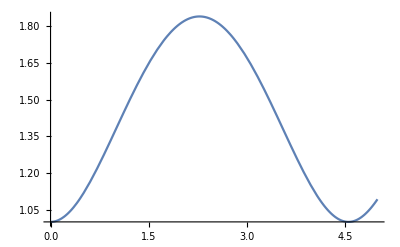

```mathematica
Plot[Evaluate[ρ[t]/.sol],{t,0,5},PlotRange->All]
```

```mathematica
t0=Pi/2;
Manipulate[ParametricPlot[{Cos@t,Sin@t},{t,t0,τ},AxesOrigin->{0,0},PlotRange->{-1.1,1.1},Epilog->{Red,PointSize[0.025],Point@{Cos@τ,Sin@τ}}],{τ,1.000001 t0,t0+2 π}]
```

ParametricPlot::plln: Limiting value t0 in {t,t0,FE`τ$$77} is not a machine-sized real number.

```mathematica
sol=NDSolve[{ρ''[t]-l0^2*v0^2/(ρ[t]^3)+k/m*(ρ[t]-l0)==0,ρ[0]==l0,ρ'[0]==0},ρ[t],{t,0,1000}];
```

```mathematica
Manipulate[PolarPlot[Evaluate[ρ[t]/.sol],{t,0,τ},AxesOrigin->{0,0},PlotRange->{{-2.5,2.5},{-2.5,2.5}},Epilog->{Red,PointSize[0.025]}],{τ,1,1000}]
```

```mathematica
y=Solve[1/2*m*(l0^2*v0^2/(r^2))+k/2(r-l0)^2==1/2*m*l0^2*v0^2,r]
```

{{r→1},{r→Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612},{r→Root-0.420-0.606 ⅈRoot[-1-#1-#1^2+#1^3&,2]-0.4196433776070806},{r→Root-0.420+0.606 ⅈRoot[-1-#1-#1^2+#1^3&,3]-0.4196433776070806}}

```mathematica
N[y]
```

{{r→1.},{r→1.83929},{r→-0.419643-0.606291 ⅈ},{r→-0.419643+0.606291 ⅈ}}

```mathematica
y[[2]][[1]][[2]]
```

Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612